# ImageVectorScope Examples

```mathematica
Information[ImageVectorscopePlot]
```

```mathematica
cardamombuns=Import["C:\\Users\\peter\\Documents\\GitHub\\data-visualization-functions\\Cardamom_buns.jpg"]
```

-Graphics-

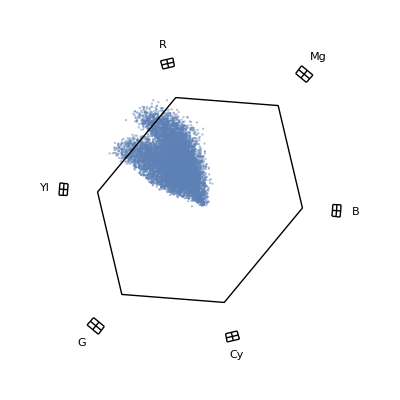

```mathematica
ImageVectorscopePlot[cardamombuns]
```

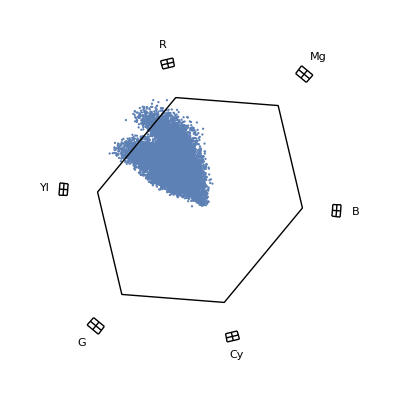

```mathematica
ImageVectorscopePlot[cardamombuns,Appearance->"Color",ImageSize->Full]
```

## File Manipulation

```mathematica
Directory[]
```

C:\Users\peter\Documents

```mathematica
SetDirectory[FileNameJoin[{Directory[],"GitHub"}]]
```

C:\Users\peter\Documents\GitHub

```mathematica
FileNames["*data*","C:\\Users\\peter\\Documents\\GitHub",IgnoreCase->True]
```

{C:\Users\peter\Documents\GitHub\data-visualization-functions,C:\Users\peter\Documents\GitHub\meteorite-data,C:\Users\peter\Documents\GitHub\poptropica-save-data,C:\Users\peter\Documents\GitHub\WikidataGeoPosition,C:\Users\peter\Documents\GitHub\wolfram-language-data-relationship-community-graph,C:\Users\peter\Documents\GitHub\word-graphs-and-graph-data}

```mathematica
FileNames["*data*visualization*",Directory[],{1},IgnoreCase->True]
```

{C:\Users\peter\Documents\GitHub\data-visualization-functions}

```mathematica
First[FileNames["*data*visualization*",Directory[],{1},IgnoreCase->True]]
```

C:\Users\peter\Documents\GitHub\data-visualization-functions

```mathematica
FileNames["*buns*","C:\\Users\\peter\\Documents\\GitHub\\data-visualization-functions"]
```

{C:\Users\peter\Documents\GitHub\data-visualization-functions\Cardamom_buns.jpg}

## Finding the picture of buns

```mathematica
FileNames["*buns*",Directory[],{2},IgnoreCase->True]
```

{C:\Users\peter\Documents\GitHub\data-visualization-functions\Cardamom_buns.jpg}

## Opening the file

```mathematica
SystemOpen[First[FileNames["*buns*",Directory[],{2},IgnoreCase->True]]]
```

```mathematica
FileNames["*data*",Directory[],{1}]
```

{C:\Users\peter\Documents\GitHub\data-visualization-functions,C:\Users\peter\Documents\GitHub\meteorite-data,C:\Users\peter\Documents\GitHub\poptropica-save-data,C:\Users\peter\Documents\GitHub\WikidataGeoPosition,C:\Users\peter\Documents\GitHub\wolfram-language-data-relationship-community-graph,C:\Users\peter\Documents\GitHub\word-graphs-and-graph-data}

```mathematica
First[FileNames["*data*",Directory[],{1}]]
```

C:\Users\peter\Documents\GitHub\data-visualization-functions

```mathematica
FileNames["*",First[FileNames["*data*",Directory[],{1}]]]
```

{C:\Users\peter\Documents\GitHub\data-visualization-functions\3D Chromaticity Diagram AdobeRGB.svg,C:\Users\peter\Documents\GitHub\data-visualization-functions\3D Chromaticity Diagram AppleRGB.svg,C:\Users\peter\Documents\GitHub\data-visualization-functions\3D Chromaticity Diagram CIERGB.svg,C:\Users\peter\Documents\GitHub\data-visualization-functions\3D Chromaticity Diagram CMYK.svg,C:\Users\peter\Documents\GitHub\data-visualization-functions\3D Chromaticity Diagram Grayscale.svg,C:\Users\peter\Documents\GitHub\data-visualization-functions\3D Chromaticity Diagram HSB.svg,C:\Users\peter\Documents\GitHub\data-visualization-functions\3D Chromaticity Diagram LAB.svg,C:\Users\peter\Documents\GitHub\data-visualization-functions\3D Chromaticity Diagram LCH.svg,C:\Users\peter\Documents\GitHub\data-visualization-functions\3D Chromaticity Diagram LUV.svg,C:\Users\peter\Documents\GitHub\data-visualization-functions\3D Chromaticity Diagram ProPhotoRGB.svg,C:\Users\peter\Documents\GitHub\data-visualization-functions\3D Chromaticity Diagram RGB.svg,C:\Users\peter\Documents\GitHub\data-visualization-functions\3D Chromaticity Diagram sRGB.svg,C:\Users\peter\Documents\GitHub\data-visualization-functions\3D Chromaticity Diagram WideGamutRGB.svg,C:\Users\peter\Documents\GitHub\data-visualization-functions\3D Chromaticity Diagram XYZ.svg,C:\Users\peter\Documents\GitHub\data-visualization-functions\Cardamom_buns.jpg,C:\Users\peter\Documents\GitHub\data-visualization-functions\Chromaticity Diagram AdobeRGB.svg,C:\Users\peter\Documents\GitHub\data-visualization-functions\Chromaticity Diagram AppleRGB.svg,C:\Users\peter\Documents\GitHub\data-visualization-functions\Chromaticity Diagram CIERGB.svg,C:\Users\peter\Documents\GitHub\data-visualization-functions\Chromaticity Diagram CMYK.svg,C:\Users\peter\Documents\GitHub\data-visualization-functions\Chromaticity Diagram Grayscale.svg,C:\Users\peter\Documents\GitHub\data-visualization-functions\Chromaticity Diagram HSB.svg,C:\Users\peter\Documents\GitHub\data-visualization-functions\Chromaticity Diagram LAB.svg,C:\Users\peter\Documents\GitHub\data-visualization-functions\Chromaticity Diagram LCH.svg,C:\Users\peter\Documents\GitHub\data-visualization-functions\Chromaticity Diagram LUV.svg,C:\Users\peter\Documents\GitHub\data-visualization-functions\Chromaticity Diagram ProPhotoRGB.svg,C:\Users\peter\Documents\GitHub\data-visualization-functions\Chromaticity Diagram RGB.svg,C:\Users\peter\Documents\GitHub\data-visualization-functions\Chromaticity Diagram sRGB.svg,C:\Users\peter\Documents\GitHub\data-visualization-functions\Chromaticity Diagram WideGamutRGB.svg,C:\Users\peter\Documents\GitHub\data-visualization-functions\Chromaticity Diagram XYZ.svg,C:\Users\peter\Documents\GitHub\data-visualization-functions\Color Vectorscope plot of hot air balloon image.svg,C:\Users\peter\Documents\GitHub\data-visualization-functions\.git,C:\Users\peter\Documents\GitHub\data-visualization-functions\.gitattributes,C:\Users\peter\Documents\GitHub\data-visualization-functions\ImageVectorScopePlot.nb,C:\Users\peter\Documents\GitHub\data-visualization-functions\README.md}

```mathematica
ReverseSortBy[FileNames["*",First[FileNames["*data*",Directory[],{1}]]],FileDate]
```

{C:\Users\peter\Documents\GitHub\data-visualization-functions\ImageVectorScopePlot.nb,C:\Users\peter\Documents\GitHub\data-visualization-functions\Cardamom_buns.jpg,C:\Users\peter\Documents\GitHub\data-visualization-functions\Color Vectorscope plot of hot air balloon image.svg,C:\Users\peter\Documents\GitHub\data-visualization-functions\3D Chromaticity Diagram WideGamutRGB.svg,C:\Users\peter\Documents\GitHub\data-visualization-functions\3D Chromaticity Diagram sRGB.svg,C:\Users\peter\Documents\GitHub\data-visualization-functions\3D Chromaticity Diagram ProPhotoRGB.svg,C:\Users\peter\Documents\GitHub\data-visualization-functions\3D Chromaticity Diagram CIERGB.svg,C:\Users\peter\Documents\GitHub\data-visualization-functions\3D Chromaticity Diagram AppleRGB.svg,C:\Users\peter\Documents\GitHub\data-visualization-functions\3D Chromaticity Diagram AdobeRGB.svg,C:\Users\peter\Documents\GitHub\data-visualization-functions\3D Chromaticity Diagram LUV.svg,C:\Users\peter\Documents\GitHub\data-visualization-functions\3D Chromaticity Diagram LCH.svg,C:\Users\peter\Documents\GitHub\data-visualization-functions\3D Chromaticity Diagram LAB.svg,C:\Users\peter\Documents\GitHub\data-visualization-functions\3D Chromaticity Diagram XYZ.svg,C:\Users\peter\Documents\GitHub\data-visualization-functions\3D Chromaticity Diagram HSB.svg,C:\Users\peter\Documents\GitHub\data-visualization-functions\3D Chromaticity Diagram CMYK.svg,C:\Users\peter\Documents\GitHub\data-visualization-functions\3D Chromaticity Diagram RGB.svg,C:\Users\peter\Documents\GitHub\data-visualization-functions\3D Chromaticity Diagram Grayscale.svg,C:\Users\peter\Documents\GitHub\data-visualization-functions\Chromaticity Diagram WideGamutRGB.svg,C:\Users\peter\Documents\GitHub\data-visualization-functions\Chromaticity Diagram sRGB.svg,C:\Users\peter\Documents\GitHub\data-visualization-functions\Chromaticity Diagram ProPhotoRGB.svg,C:\Users\peter\Documents\GitHub\data-visualization-functions\Chromaticity Diagram CIERGB.svg,C:\Users\peter\Documents\GitHub\data-visualization-functions\Chromaticity Diagram AppleRGB.svg,C:\Users\peter\Documents\GitHub\data-visualization-functions\Chromaticity Diagram AdobeRGB.svg,C:\Users\peter\Documents\GitHub\data-visualization-functions\Chromaticity Diagram LUV.svg,C:\Users\peter\Documents\GitHub\data-visualization-functions\Chromaticity Diagram LCH.svg,C:\Users\peter\Documents\GitHub\data-visualization-functions\Chromaticity Diagram LAB.svg,C:\Users\peter\Documents\GitHub\data-visualization-functions\Chromaticity Diagram XYZ.svg,C:\Users\peter\Documents\GitHub\data-visualization-functions\Chromaticity Diagram HSB.svg,C:\Users\peter\Documents\GitHub\data-visualization-functions\Chromaticity Diagram CMYK.svg,C:\Users\peter\Documents\GitHub\data-visualization-functions\Chromaticity Diagram RGB.svg,C:\Users\peter\Documents\GitHub\data-visualization-functions\Chromaticity Diagram Grayscale.svg,C:\Users\peter\Documents\GitHub\data-visualization-functions\.git,C:\Users\peter\Documents\GitHub\data-visualization-functions\README.md,C:\Users\peter\Documents\GitHub\data-visualization-functions\.gitattributes}

```mathematica
TakeLargestBy[FileNames["*",First[FileNames["*data*",Directory[],{1}]]],FileDate,3]
```

{C:\Users\peter\Documents\GitHub\data-visualization-functions\ImageVectorScopePlot.nb,C:\Users\peter\Documents\GitHub\data-visualization-functions\Cardamom_buns.jpg,C:\Users\peter\Documents\GitHub\data-visualization-functions\Color Vectorscope plot of hot air balloon image.svg}

### Finding the Image Scope file

```mathematica
SystemOpen[First[TakeLargestBy[FileNames["*",First[FileNames["*data*",Directory[],{1}]]],FileDate,3]]]
```

## Importing the bun file

```mathematica
Import[First[FileNames["*buns*",Directory[],{2},IgnoreCase->True]]]
```

-Graphics-

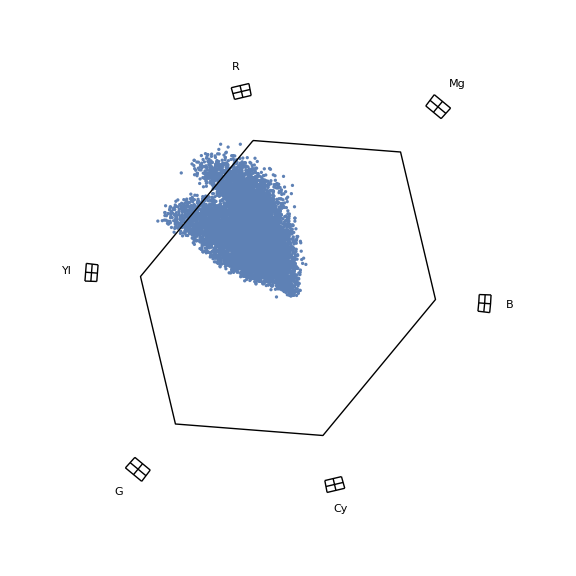

```mathematica
ImageVectorscopePlot[Import[First[FileNames["*buns*",Directory[],{2},IgnoreCase->True]]],Appearance->"Color",ImageSize->Large]
```

```mathematica
Directory[]
```

C:\Users\peter\Documents\GitHub

```mathematica
Names["*Directory*"]
```

```mathematica
{"AddDocumentationDirectory","ApplicationDataDirectory","ApplicationDataUserDirectory","ApplicationDirectoryAdd","CloudDirectory","CopyDirectory","CreateDataDirectory","CreateDirectory","DeleteDirectory","Directory","DirectoryName","DirectoryQ","DirectoryStack","HomeDirectory","NotebookBrowseDirectory","NotebookDirectory","PacletDirectoryAdd","PacletDirectoryLoad","PacletDirectoryRemove","PacletDirectoryUnload","ParentDirectory","ProcessDirectory","RenameDirectory","ResetDirectory","SetCloudDirectory","SetDirectory","$AddOnsDirectory","$BaseDirectory","$BasePacletsDirectory","$CacheBaseDirectory","$CloudRootDirectory","$HomeDirectory","$InitialDirectory","$InstallationDirectory","$LaunchDirectory","$PreferencesDirectory","$RootDirectory","$TemporaryDirectory","$TopDirectory","$UserAddOnsDirectory","$UserBaseDirectory","$UserBasePacletsDirectory","$UserDocumentsDirectory","$WolframDocumentsDirectory"}
```

```mathematica
NotebookDirectory[]
```

C:\Users\peter\Documents\GitHub\data-visualization-functions\

```mathematica
FileNameJoin[{NotebookDirectory[],"cardamom buns image vector scope plot color"}]
```

C:\Users\peter\Documents\GitHub\data-visualization-functions\cardamom buns image vector scope plot color

## Exporting the file

```mathematica
Export[File[FileNameJoin[{NotebookDirectory[],"cardamom buns image vector scope plot color.svg"}]],ImageVectorscopePlot[Import[First[FileNames["*buns*",Directory[],{2},IgnoreCase->True]]],Appearance->"Color",ImageSize->Large]]
```

C:\Users\peter\Documents\GitHub\data-visualization-functions\cardamom buns image vector scope plot color.svg

```mathematica
SystemOpen["C:\\Users\\peter\\Documents\\GitHub\\data-visualization-functions\\cardamom buns image vector scope plot color.svg"]
```

```mathematica
Information[ImageVectorscopePlot]
```

## Finding Cantor Dust file

```mathematica
FileNames["*Cantor*",Directory[],4]
```

{C:\Users\peter\Documents\GitHub\function-repository\CantorDust.nb}